## QCD Phase Transition in chiral limit with new fermionic vacuum term

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Constants, all energies in Gev*)
Nc=3;
Nf=2;
Ns=2;
Deg=Ns Nc Nf;
mq=0.335;
msig=0.570;
mpi=0.138;
fpi=0.093;
Lam=10;(*=infinity, results mostly independent for Lam>>msig*)
g=mq/fpi;
M=0.5;
eps0=0;
```

```mathematica
lam[eps_]:=(3*Deg*fpi^3*g^4-8*(eps-fpi*msig^2)*Pi^2+4*Deg*fpi^3*g^4*Log[(fpi*g)/M])/(16*fpi^3*Pi^2)
V2[eps_]:=(2*fpi^2*(Deg*fpi^3*g^4+4*(-3*eps+fpi*msig^2)*Pi^2))/(3*Deg*fpi^3*g^4-8*(eps-fpi*msig^2)*Pi^2+4*Deg*fpi^3*g^4*Log[(fpi*g)/M])
```

```mathematica
eps0
lam[eps0]
V2[eps0]
```

0

36.6698

0.0104653

```mathematica
(*Energy in dependence on sig and P*)
En[p_,sig_]:=Sqrt[p^2+g^2 sig^2];
```

```mathematica
(*Fermionic Pressure*)
int[sig_,T_,mu_]:=p^2(T Log[1+Exp[(mu-En[p,sig])/T]]+T Log[1+Exp[-(mu+En[p,sig])/T]])
vac[sig_]:=Deg/(16 Pi^2) g^4sig^4 Log[sig g/M]
PF[sig_,T_,mu_]:=vac[sig]+Deg/(2Pi^2)NIntegrate[int[sig,T,mu],{p,0,Lam}]
(*Bosonic pressure*)
PB[sig_,eps_]:=-lam[eps]/4(sig^2-V2[eps])^2+eps sig
(*Altogether*)
Pa[sig_,eps_,T_,mu_]:=PF[sig,T,mu]+PB[sig,eps]
```

```mathematica
(*Derivatives in respect to sig*)
vac1[sig_]=D[vac[sigs],{sigs,1}]/.sigs->sig//Simplify;
vac2[sig_]=D[vac[sigs],{sigs,2}]/.sigs->sig//Simplify;
vac3[sig_]=D[vac[sigs],{sigs,3}]/.sigs->sig//Simplify;
vac4[sig_]=D[vac[sigs],{sigs,4}]/.sigs->sig//Simplify;
int1[sig_,T_,mu_]=D[int[sigs,T,mu],{sigs,1}]/.sigs->sig;
int2[sig_,T_,mu_]=D[int[sigs,T,mu],{sigs,2}]/.sigs->sig;
int3[sig_,T_,mu_]=D[int[sigs,T,mu],{sigs,3}]/.sigs->sig;
int4[sig_,T_,mu_]=D[int[sigs,T,mu],{sigs,4}]/.sigs->sig;
PB1[sig_,eps_]=D[PB[sigs,eps],{sigs,1}]/.sigs->sig//Simplify;
PB2[sig_,eps_]=D[PB[sigs,eps],{sigs,2}]/.sigs->sig//Simplify;
PB3[sig_,eps_]=D[PB[sigs,eps],{sigs,3}]/.sigs->sig//Simplify;
PB4[sig_,eps_]=D[PB[sigs,eps],{sigs,4}]/.sigs->sig//Simplify;
Pder1[sig_,eps_,T_,mu_]:=vac1[sig]+Deg/(2Pi^2)NIntegrate[int1[sig,T,mu],{p,0,Lam}]+PB1[sig,eps]
Pder2[sig_,eps_,T_,mu_]:=vac2[sig]+Deg/(2Pi^2)NIntegrate[int2[sig,T,mu],{p,0,Lam}]+PB2[sig,eps]
Pder3[sig_,eps_,T_,mu_]:=vac3[sig]+Deg/(2Pi^2)NIntegrate[int3[sig,T,mu],{p,0,Lam}]+PB3[sig,eps]
Pder4[sig_,eps_,T_,mu_]:=vac4[sig]+Deg/(2Pi^2)NIntegrate[int4[sig,T,mu],{p,0,Lam}]+PB4[sig,eps]
```

```mathematica
(*Derivatives in respect to mu (baryon number susceptibility)*)
int1mu[sig_,T_,mu_]=D[int[sig,T,mus],{mus,1}]/.mus->mu;
int2mu[sig_,T_,mu_]=D[int[sig,T,mus],{mus,2}]/.mus->mu;
Pder1mu[sig_,eps_,T_,mu_]:=Deg/(2Pi^2)NIntegrate[int1mu[sig,T,mu],{p,0,Lam}]
Pder2mu[sig_,eps_,T_,mu_]:=Deg/(2Pi^2)NIntegrate[int2mu[sig,T,mu],{p,0,Lam}]
```

```mathematica
(*Mixed derivatives in respect to mu and sig*)
int2musig[sig_,T_,mu_]=D[int1mu[sigs,T,mu],{sigs,1}]/.sigs->sig;
int2sigmu[sig_,T_,mu_]=D[int1[sig,T,mus],{mus,1}]/.mus->mu;
Pder2sigmu[sig_,eps_,T_,mu_]:=Deg/(2Pi^2)NIntegrate[int2sigmu[sig,T,mu],{p,0,Lam}]
```

```mathematica
(*The maximum for T=0 and mu=0 must be at sig=fpi*)
sig/.FindRoot[Pder1[sig,eps0,0.005,0]==0,{sig,0.1}]//Quiet
```

0.093

```mathematica
(*Limits*)
steplow=10;
mum=0;mup=0.4;Tm=0.005;Tp=0.20;step=200;sig0=0.0001;
(*Helper functions*)
(*get a real number for a given integer representing mu, or get an integer number for a given real mu*)
muQ[muN_]:=mum+(muN-1)*(mup-mum)/step
muI[muQ_]:=IntegerPart[(muQ-mum)/(mup-mum)step+1]
(*Same for temperature*)
TQ[TN_]:=Tm+(TN-1)*(Tp-Tm)/step
TI[TQ_]:=IntegerPart[(TQ-Tm)/(Tp-Tm)step+1]
```

```mathematica
(*Find the tricritical point (TCP), h=0, sigstar=0*)
repl[eps_]:=FindRoot[{Pder2[sig0,eps,T,mu]==0,Pder4[sig0,eps,T,mu]==0},{{T,0.075},{mu,0.27}}]//Quiet
repl0=repl[eps0];
sigTCP=sig0
TTCP=T/.repl0
muTCP=mu/.repl0
```

0.0001

0.0762774

0.27957

```mathematica
(*find the tricritical point more precisely (from Gabor: Expansion.nb)*)
m4[T_,μ_]:=Simplify[(1/(16*Pi^2))*(3/4+Log[4]+(1/2)*(PolyGamma[0,1/2-(I*μ)/(2*Pi*T)]+PolyGamma[0,1/2+(I*μ)/(2*Pi*T)]))];
m4full[T_,μ_]:=Deg*m4[T,μ]*g^4-lam[eps0]/4+(Deg/(16*Pi^2))*Log[(Pi*T)/M]*g^4;
muTCP=Re[mu/.FindRoot[m4full[Sqrt[(12 lam[eps0] Pi^2 V2[eps0]-3Deg g^2 mu^2)/(Deg g^2 Pi^2)],mu],{mu,0.26}]]
TTCP=Sqrt[(12 lam[eps0] Pi^2 V2[eps0]-3Deg g^2 muTCP^2)/(Deg g^2 Pi^2)]
```

0.27957

0.0762778

```mathematica
(*critical temperature for 2nd order phase transition in dependence of mu, analytical form*)
Tc2nd[mu_,eps_]:=Sqrt[(12 lam[eps] Pi^2 V2[eps]-3Deg g^2 mu^2)/(Deg g^2 Pi^2)]
```

```mathematica
(*test the results*)
Pder2[sigTCP,eps0,TTCP,muTCP]//Quiet
Pder4[sigTCP,eps0,TTCP,muTCP]//Quiet
Tc2nd[muTCP,eps0]
```

-7.65221×10^-13

-0.000725731

0.0762778

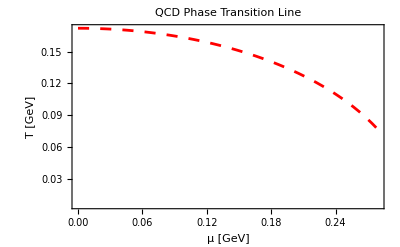

```mathematica
(*plot critical temp. in dependence of mu*)
plotTc2nd=Plot[{Tc2nd[mu,eps0]},{mu,0,muTCP},AxesLabel->{"mu","T"},PlotStyle->{Dashing[0.02],Red,Thickness[0.005]},AxesOrigin->{mum,Tm},FrameLabel->{"μ [GeV]","T [GeV]"},
LabelStyle->{FontSize->18},
PlotLabel->Text[Style["QCD Phase Transition Line",FontSize->18]],Frame->True]
```

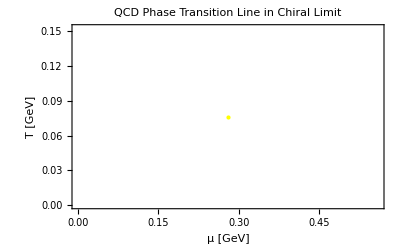

```mathematica
(*plot critical point*)
critPoint=ListPlot[{{muTCP,Tc2nd[muTCP,eps0]}},PlotStyle->Directive[PointSize[Large],Yellow],AxesLabel->{"mu","T"},FrameLabel->{"μ [GeV]","T [GeV]"},
LabelStyle->{FontSize->18},
PlotLabel->Text[Style["QCD Phase Transition Line in Chiral Limit",FontSize->18]],Frame->True]
```

```mathematica
(*Determine the position of the pressure maxima (sigstar) in dependence on T and mu*)
root1[eps_,T_,mu_]:=sig/.FindRoot[Pder1[sig,eps,T,mu]==0,{sig,0.1}]
root2[eps_,T_,mu_]:=sig/.FindRoot[Pder1[sig,eps,T,mu]==0,{sig,0.001}]
sigstar[eps_,T_,mu_]:=Re[If[Re[Pa[(sig1=root1[eps,T,mu]),eps,T,mu]]>Re[Pa[(sig2=root2[eps,T,mu]),eps,T,mu]],sig1,sig2]]//Quiet
```

```mathematica
(*test*)
sigstar[eps0,0.05,0.4]
```

9.0344×10^-19

```mathematica
(*generate the table*)
(*tabsigstar200=Table[{mu,T,sigstar[eps0,T,mu]},{mu,mum,mup,(mup-mum)/step},{T,Tm,Tp,(Tp-Tm)/step}];
Export["tabsigstar200_nfp.wdx",tabsigstar200,"WDX"];*)
```

```mathematica
tabsigstar=Import["tabsigstar200_nfp.wdx"];
```

```mathematica
(*Density plot of the order parameter*)
(*densityPlotSig=ListDensityPlot[Flatten[tabsigstar,1],FrameLabel->{"μ [GeV]","T [GeV]"},ColorFunction->"SolarColors",LabelStyle->{FontSize->18},PlotLabel->Text[Style["QCD Phase Diagram in chiral limit",FontSize->18]]];
Export["densityPlotSig200_nfp.wdx",densityPlotSig,"WDX"];*)
```

```mathematica
densityPlotSigImp=Import["densityPlotSig200_nfp.wdx"]
```

-Graphics-

```mathematica
(*phase border for the 1st order transition*)
(*threshold=-5*10^(-9);
fn[muN_,TN_]:=-Abs[Pa[sig0,eps0,TQ[TN],muQ[muN]]-Pa[tabsigstar[[muN]][[TN]][[3]],eps0,TQ[TN],muQ[muN]]]
fnlist[muN_]:=Table[fn[muN,TN],{TN,1,step}]
positionZero[muN_]:=Flatten[Position[fnlist[muN],Select[fnlist[muN],#≥threshold&,1][[1]]],2][[1]]
Tc1stlist200=Table[{muQ[muN],TQ[positionZero[muN]]},{muN,muI[muTCP]+1,muI[0.33]-1}];
Export["Tc1stlist200_nfp.wdx",Tc1stlist200,"WDX"];*)
```

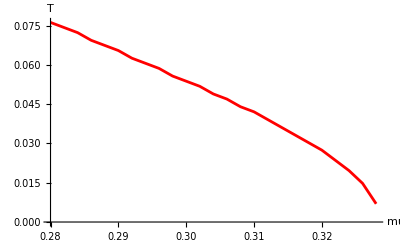

```mathematica
Tc1stlist=Import["Tc1stlist200_nfp.wdx"];
plotTc1st=ListPlot[Tc1stlist,AxesLabel->{"mu","T"},Joined->True,PlotStyle->{Red,Thickness[0.005]}]
```

```mathematica
(*Plot overall phase diagram*)
text=Show[Graphics[{Yellow,FontSize->18,Text["TCP",{muTCP+0.02,TTCP}]}],Graphics[{Yellow,FontSize->18,Text["2nd",{muTCP-0.05,TTCP+0.06}]}],Graphics[{Yellow,FontSize->18,Text["1st",{muTCP+0.05,TTCP-0.035}]}]];
lines=Show[plotTc2nd,plotTc1st,critPoint,PlotRange->{{mum,mup},{Tm,Tp}},AxesOrigin->{mum,Tm},ImageSize->{600,400}];
Export["PhaseTransitionLine_nfp.wdx",lines,"WDX"];
PhaseTransitionDensity=Show[{densityPlotSigImp,plotTc2nd,plotTc1st,critPoint,text},PlotRange->{{mum,mup},{Tm,Tp}},AxesOrigin->{mum,Tm},ImageSize->{500,500}]
Export["PhaseTransitionDensity_nfp.wdx",PhaseTransitionDensity,"WDX"];
```

-Graphics-

## Baryon Number Susceptibility on lines going through TCP

```mathematica
(*The scaling coefficient will be important around t=0, so choose for the fit only points in a narrow region around t=0*)
choose=-20;(*choose=All*)
```

```mathematica
Clear[sigs]
```

```mathematica
(*Baryon number susceptibility in respect to sig, eps, T, mu*)
chiB[eps_,T_,mu_]:=Pder2mu[sigs=sigstar[eps,T,mu],eps,T,mu]-Pder2sigmu[sigs,eps,T,mu]^2(Pder2[sigs,eps,T,mu])^(-1)
```

```mathematica
chiB[eps0,TTCP+0.1,muTCP]
Clear[sigs]
chiB[eps0,TTCP,muTCP]
chiB[eps0,TTCP+0.1,muTCP]
```

0.109663+1.02261×10^-92 ⅈ

0.0591518+1.67222×10^-18 ⅈ

0.109663+1.02261×10^-92 ⅈ

```mathematica
(*Density plot of the baryon number susc. for h=0*)
(*step=200;
chiBlist0=Flatten[Table[{mu,T,Re[chiB[eps0,T,mu]]},{T,Tm,Tp,(Tp-Tm)/step},{mu,mum,mup,(mup-mum)/step}],1]//Quiet;
Export["chiBlist0_nfp.wdx",chiBlist0,"WDX"];*)
```

```mathematica
chiBlist0=Import["chiBlist0_nfp.wdx"];
```

```mathematica
LogarithmicScaling[x_,min_,max_]:=Log[x/min]/Log[max/min]
plotter[min_,max_,NumberOfTicks_]:=ListDensityPlot[Re[chiBlist0],PlotRange->Full,ColorFunctionScaling->False,ColorFunction->(ColorData["LightTemperatureMap"][LogarithmicScaling[#,min,max]]&),FrameLabel->{"μ [GeV]","T [GeV]"},LabelStyle->{FontSize->16},PlotLabel->Text[Style["Baryon number susceptibility for h=0",FontSize->16]],ImageSize->{400,400},PlotLegends->BarLegend[{ColorData["LightTemperatureMap"],{0,1}},LegendMarkerSize->370,Ticks->({LogarithmicScaling[#,min,max],ScientificForm[#,2]}&/@(min (max/min)^Range[0,1,1/NumberOfTicks])),LabelStyle->{FontSize->16}]]
```

```mathematica
(*logdensityPlotChiB=plotter[0.001,100,5]
logdensityPlotChiBRasterized=Rasterize[logdensityPlotChiB,RasterSize->1000];
Export["chiBLogPlot0_nfp.wdx",logdensityPlotChiBRasterized,"WDX"];
Export["chiBLogPlot0_nfp.pdf",logdensityPlotChiBRasterized,"PDF"];*)
```

```mathematica
logdensityPlotChiBRasterized=Import["chiBLogPlot0_nfp.wdx"]
```

-Graphics-

### Baryon number susceptibility on the line μ=μ_TCP

```mathematica
(*Baryon number Susceptibility near the TCP for eps=0 and μ=Subscript[μ, TCP]*)
step=400;
chiBlist0muTCP=Table[{(T-TTCP)/TTCP,Re[chiB[eps0,T,muTCP]]},{T,Tm,1.5TTCP,(1.5TTCP-Tm)/step}];
Export["chiBlist0_muTCP_nfp.wdx",chiBlist0muTCP,"WDX"];
```

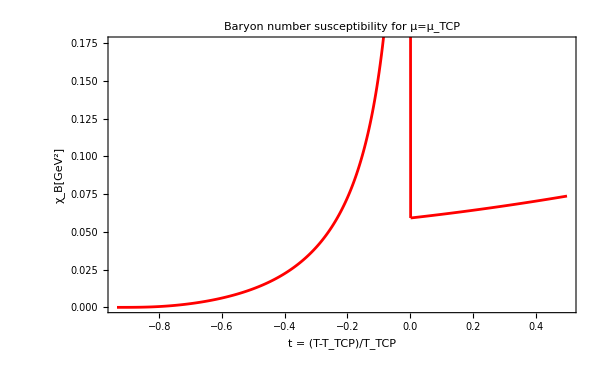

```mathematica
(*Plot the results for mu=muTCP*)
chiBlist0muTCP=Import["chiBlist0_muTCP_nfp.wdx"];
plot=ListPlot[{chiBlist0muTCP},FrameLabel->{"t = (T-T_TCP)/T_TCP","χ_B[GeV^2]"},LabelStyle->{FontSize->16},Joined->True,Frame->True,PlotLabel->Style["Baryon number susceptibility for μ=μ_TCP",FontSize->18],ImageSize->{600,400},PlotStyle->{Directive[Red,AbsoluteThickness[2]]}]
Export["chiBlist0_muTCP_nfp.pdf",plot,"PDF"];
```

```mathematica
(*Fit the susc. for t<0 to determine the scaling coefficient β*)
step=400;
model=α t^(-β);
fit0muTCP=FindFit[Abs[Take[Take[chiBlist0muTCP,261],-5]],model,{α,β},t]
```

{α→0.0595529,β→0.556924}

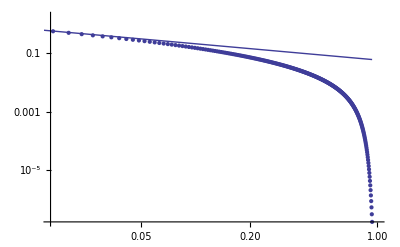

```mathematica
(*Test the fit. Note that the x-axis is now inverted and positive*)
Show[{ListLogLogPlot[{Abs[Take[chiBlist0muTCP,261]]}],LogLogPlot[{model/.fit0muTCP},{t,0.002,-(Tm-TTCP)/TTCP}]}]
```

### Baryon number susceptibility on the line T=T_TCP

```mathematica
(*Baryon number Susceptibility near the TCP for eps=0 and T=Subscript[T, TCP]*)
step=400;
chiBlist0TTCP=Table[{(mu-muTCP)/muTCP,chiB[eps0,TTCP,mu]},{mu,mum,mup,(mup-mum)/step}]//Quiet;
Export["chiBlist0_TTCP_nfp.wdx",chiBlist0TTCP,"WDX"];
```

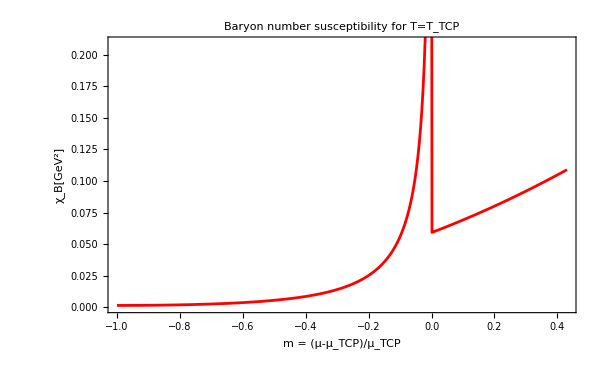

```mathematica
(*Plot the results for mu=muTCP*)
chiBlist0TTCP=Import["chiBlist0_TTCP_nfp.wdx"];
plot=ListPlot[{chiBlist0TTCP},FrameLabel->{"m = (μ-μ_TCP)/μ_TCP","χ_B[GeV^2]"},LabelStyle->{FontSize->16},Joined->True,Frame->True,PlotLabel->Style["Baryon number susceptibility for T=T_TCP",FontSize->18],ImageSize->{600,400},PlotStyle->{Directive[Red,AbsoluteThickness[2]]}]
Export["chiBlist0_TTCP_nfp.pdf",plot,"PDF"];
```

```mathematica
(*Fit the susc. for t<0 to determine the scaling coefficient β*)
step=400;
model=α m^(-β);
fit0TTCP=FindFit[Abs[Take[Take[chiBlist0TTCP,muI[muTCP]],-5]],model,{α,β},m]
```

{α→0.0215164,β→0.598436}

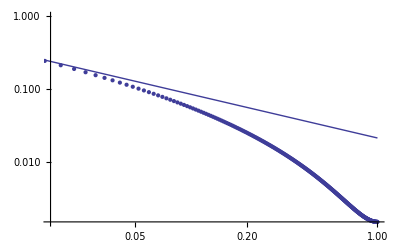

```mathematica
(*Test the fit. Note that the x-axis is now inverted and positive*)
Show[{ListLogLogPlot[{Abs[Take[chiBlist0TTCP,muI[muTCP]]]}],LogLogPlot[{model/.fit0TTCP},{m,0.0005,-(mum-muTCP)/muTCP}]}]
```

### Baryon number susceptibility on the 2nd order phase border line

```mathematica
(*Baryon number Susceptibility near the TCP for eps=0 on the 2nd order phase border line*)
step=100;
epsilon=-0.0001;
chiBlist02nd=Table[{(Tc2nd[mu,eps0]-TTCP)/TTCP,chiB[eps0,Tc2nd[mu,eps0]-(mu-muTCP)epsilon,mu]},{mu,mum,muTCP,(muTCP-mum)/step}]//Quiet;
Export["chiBlist0_2nd_nfp.wdx",chiBlist02nd,"WDX"];
```

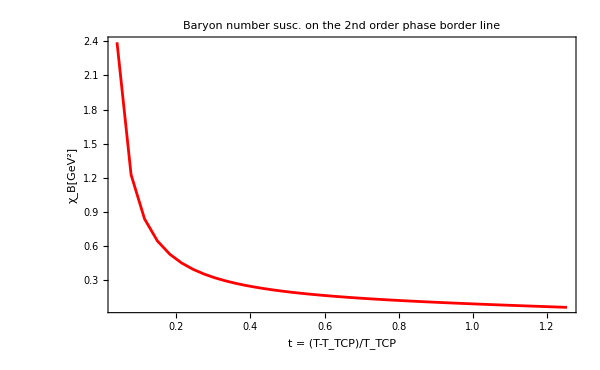

```mathematica
(*Plot the results*)
chiBlist02nd=Import["chiBlist0_2nd_nfp.wdx"];
plot=ListPlot[{Take[Re[chiBlist02nd],100]},FrameLabel->{"t = (T-T_TCP)/T_TCP","χ_B[GeV^2]"},LabelStyle->{FontSize->16},Joined->True,Frame->True,PlotLabel->Style["Baryon number susc. on the 2nd order phase border line",FontSize->18],ImageSize->{600,400},PlotRange->All,PlotStyle->{Directive[Red,AbsoluteThickness[2]]}]
Export["chiBlist0_Ta0_nfp.pdf",plot,"PDF"];
```

```mathematica
(*Fit the susc. for t<0 to determine the scaling coefficient β*)
model=α t^(-β);
fit01st=FindFit[Abs[Take[Take[Re[chiBlist02nd3],100],-20]],model,{α,β},t]
```

{α→0.0977331,β→0.991785}

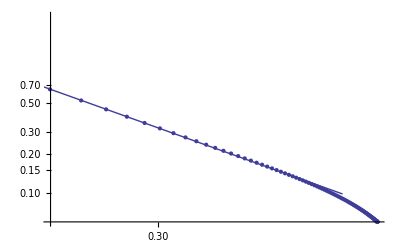

```mathematica
(*Test the fit. Note that the x-axis is now inverted and positive*)
Show[{ListLogLogPlot[{Abs[Take[Take[chiBlist02nd3,100],All]]}],LogLogPlot[{model/.fit01st},{t,0.001,1}]}]
```

### All scaling coefficients at a clance (χ_B ~.1d t^-β, χ_B ~.1d m^-β )

```mathematica
(*all scaling coefficients at a glance*)
(*for the coefficients for h=h0 we do not expect a special scaling, since for finite h there is no divergency in the TCP.*)
step=200;
tab2={{β/.fit0muTCP,β/.fit0TTCP,β/.fit01st}};
TableForm[tab2,TableHeadings->{{"ϵ=0"},{"T=T_(μ = SubscriptBox[μ, TCP])","T=T_TCP","T=T_(a = 0)"}}]
```

| T=T_(μ = SubscriptBox[μ, TCP]) | T=T_TCP | T=T_(a = 0)
ϵ=0 | 0.556924 | 0.598436 | 0.991785